Interpolacja punktów c_D od Re:

```mathematica
dane={{0.2,103},{2,13.9},{20,2.72},{200,0.8},{2000,0.401},{20000,0.433}};
g1=Interpolation[dane]
```

InterpolatingFunction[{{0.2, 20000.}}, <>]

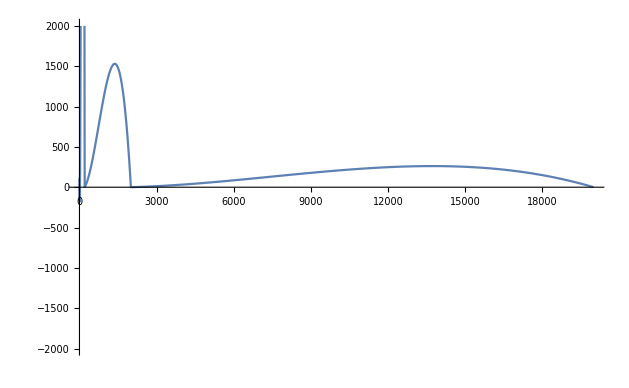

```mathematica
Plot[g1[x],{x, 0, 20000},PlotRange->2000]
```

Wartości funkcji w Re = 5, 50, 5000

```mathematica
g1[5]
```

-96.3863

```mathematica
g1[50]
```

2653.98

```mathematica
g1[5000]
```

56.8063

Sklejanie za pomocą B-Spline Function

```mathematica
g2=BSplineFunction[dane]
```

BSplineFunction[{{0., 1.}}, <>]

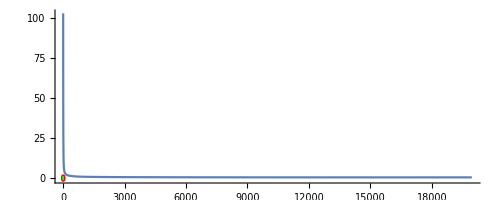

```mathematica
Show[Graphics[{Red,Point[pts],Green,Line[pts]},Axes->True],ParametricPlot[f2[x],{x,0,50}]]
```

można to też policzyć ręcznie równania funkcji sklejanych (do dokończenia):

```mathematica
fun[x_]:= a*x^3 + b*x^2 +c*x + d
```

```mathematica
fun'[x]
```

c+2 b x+3 a x^2

```mathematica
fun''[x]
```

2 b+6 a x